```mathematica
b∈{1,2,3}
0<i
0≤j
```

```mathematica
a(i*{0})b(j*{0})==a*4^(i+j)+b*4^j+(0≤c<4^j)+d*4^(i+j+1)
```

```mathematica
(0<a)4^(i+1)+(0<b<4^i)
0<i
```

```mathematica
gd[x_]:=(Times@@IntegerDigits[x/(4^IntegerExponent[x,4]),4])≠0
```

```mathematica
Table[{i,try[i],gd[i]},{i,1,10}]
```

{{1,True,True},{2,True,True},{3,True,True},{4,True,True},{5,False,True},{6,True,True},{7,True,True},{8,True,True},{9,False,True},{10,False,True}}

```mathematica
Select[Range[100],gd]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,20,21,22,23,24,25,26,27,28,29,30,31,32,36,37,38,39,40,41,42,43,44,45,46,47,48,52,53,54,55,56,57,58,59,60,61,62,63,64,80,84,85,86,87,88,89,90,91,92,93,94,95,96,100}

```mathematica
IntegerDigits[21,4]
```

{1,1,1}

```mathematica
gf[n_]:=Block[{sofar=0,pos=0},
Do[If[gd[i],sofar+=i*x^pos;pos++,0],{i,1,n}];sofar]
```

```mathematica
egf[n_]:=Monitor[Block[{sofar=0,pos=0},
Do[If[gd[i],sofar+=i*x^pos/pos!;pos++,0],{i,1,n}];sofar],i]
```

```mathematica
cgf=gf[20000];
```

```mathematica
cegf=egf[10000];
```

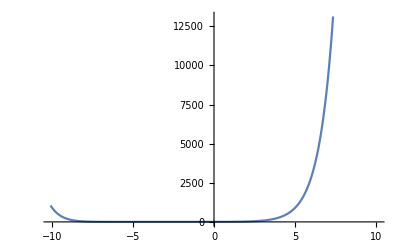

```mathematica
Plot[cegf,{x,-10.1,10.1}]
```

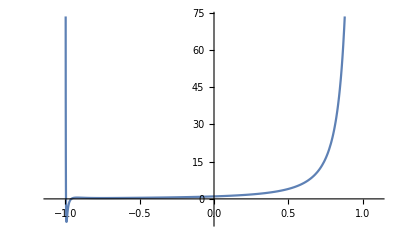

```mathematica
Plot[cgf,{x,-1.1,1.1}]
```

```mathematica
ngf[n_]:=Monitor[Block[{sofar=0,pos=0},
Do[If[¬gd[i],sofar+=i*x^pos;pos++],{i,1,n}];sofar],i]
```

```mathematica
cngf=ngf[50000];
```

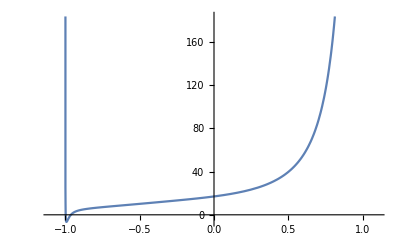

```mathematica
Plot[cngf,{x,-1.1,1.1}]
```

```mathematica
ng[n_]:=ng[n]=If[n==1,17,Block[{p=ng[n-1]+1},While[gd[p],p++];p]]
```

```mathematica
Table[ng[i],{i,200,300}]
```

{456,457,458,459,460,461,462,463,465,466,467,481,482,483,497,498,499,513,514,515,516,517,518,519,520,521,522,523,524,525,526,527,528,529,530,531,532,533,534,535,536,537,538,539,540,541,542,543,544,545,546,547,548,549,550,551,552,553,554,555,556,557,558,559,560,561,562,563,564,565,566,567,568,569,570,571,572,573,574,575,577,578,579,580,581,582,583,584,585,586,587,588,589,590,591,593,594,595,609,610,611}

```mathematica
FindSequenceFunction[Table[ng[i],{i,1,200}],x]
```

FindSequenceFunction[{17,18,19,33,34,35,49,50,51,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,81,82,83,97,98,99,113,114,115,129,130,131,132,133,134,135,136,137,138,139,140,141,142,143,145,146,147,161,162,163,177,178,179,193,194,195,196,197,198,199,200,201,202,203,204,205,206,207,209,210,211,225,226,227,241,242,243,257,258,259,260,261,262,263,264,265,266,267,268,269,270,271,272,273,274,275,276,277,278,279,280,281,282,283,284,285,286,287,288,289,290,291,292,293,294,295,296,297,298,299,300,301,302,303,304,305,306,307,308,309,310,311,312,313,314,315,316,317,318,319,321,322,323,324,325,326,327,328,329,330,331,332,333,334,335,337,338,339,353,354,355,369,370,371,385,386,387,388,389,390,391,392,393,394,395,396,397,398,399,401,402,403,417,418,419,433,434,435,449,450,451,452,453,454,455,456},x]

```mathematica
5*60
```

300

```mathematica
FindGeneratingFunction[Table[ng[i],{i,1,100}],x,TimeConstraint->500]
```

FindGeneratingFunction[{17,18,19,33,34,35,49,50,51,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,81,82,83,97,98,99,113,114,115,129,130,131,132,133,134,135,136,137,138,139,140,141,142,143,145,146,147,161,162,163,177,178,179,193,194,195,196,197,198,199,200,201,202,203,204,205,206,207,209,210,211,225,226,227,241,242,243,257,258,259,260,261,262,263,264,265,266,267,268,269,270,271,272,273,274,275},x,TimeConstraint→500]

```mathematica
StringJoin[Map[StringJoin[ToString[#]," "]&,Table[ng[i],{i,1,100}]]]
```

17 18 19 33 34 35 49 50 51 65 66 67 68 69 70 71 72 73 74 75 76 77 78 79 81 82 83 97 98 99 113 114 115 129 130 131 132 133 134 135 136 137 138 139 140 141 142 143 145 146 147 161 162 163 177 178 179 193 194 195 196 197 198 199 200 201 202 203 204 205 206 207 209 210 211 225 226 227 241 242 243 257 258 259 260 261 262 263 264 265 266 267 268 269 270 271 272 273 274 275

17+18 x+19 x^2+33 x^3+(x^4 (34-33 x+13 x^2-13 x^3+13 x^5-13 x^6))/(-1+x)^2

```mathematica
SeriesCoefficient[(17+x+x^2-3 x^3)/((-1+x)^2 (1+x+x^2)),{x,0,100}]
```

546

```mathematica
Flatten[Table[If[¬gd[i],i,{}],{i,1,23}]]
```

{17,18,19}

```mathematica
fixIA[a_,i_]:=If[(a<1)∨(i<1),{},Table[a*4^(i+1)+b,{b,1,4^i-1}]]
```

```mathematica
gfixIA[a_,i_]:=If[(a<1)∨(i<1),{},Table[(a*4^(i+1)+b),{b,1,4^i-1}]]
```

```mathematica
fixIA[2,1]
```

{33,34,35}

```mathematica
fixIA[a1,b1]< fixIA[a2,b2]⇔(b1<b2)∨((b1==b2)∧(a1<a2))
```

```mathematica
Sort[Flatten[Table[{i,j},{j,1,8},{i,1,8}],1]]
```

{{1,1},{1,2},{1,3},{1,4},{1,5},{1,6},{1,7},{1,8},{2,1},{2,2},{2,3},{2,4},{2,5},{2,6},{2,7},{2,8},{3,1},{3,2},{3,3},{3,4},{3,5},{3,6},{3,7},{3,8},{4,1},{4,2},{4,3},{4,4},{4,5},{4,6},{4,7},{4,8},{5,1},{5,2},{5,3},{5,4},{5,5},{5,6},{5,7},{5,8},{6,1},{6,2},{6,3},{6,4},{6,5},{6,6},{6,7},{6,8},{7,1},{7,2},{7,3},{7,4},{7,5},{7,6},{7,7},{7,8},{8,1},{8,2},{8,3},{8,4},{8,5},{8,6},{8,7},{8,8}}

```mathematica
Map[Last,Sort[Flatten[Table[{fixIA[i,j],{i,j}},{i,1,16},{j,1,16}],1]]]
```

$Aborted

```mathematica
IntegerDigits[4^2+4,4]
```

{1,1,0}

```mathematica
Monitor[DeleteDuplicates[Differences[Table[ng[i],{i,1,5000000}]]]//Sort,i]
```

{1,2,14}

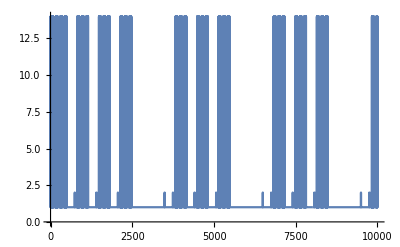

```mathematica
Differences[Table[ng[i],{i,1,10000}]]//ListPlot[#,Joined->True,PlotRange->All]&
```

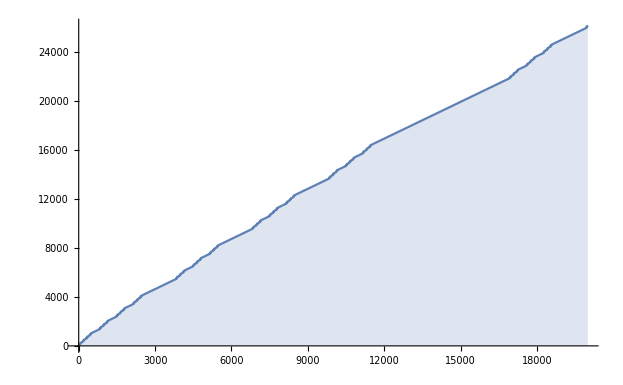

```mathematica
DiscretePlot[ng[i],{i,1,20000}]
```

```mathematica
fs=List[1,1,1,2,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,6,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,6,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,6,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,7,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,6,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,6,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,7,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,6,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,6,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,7,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,6,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,6,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,8,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,6,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,6,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,7,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,6,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,6,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,7,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,6,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,6,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,8,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,6,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,6,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,7,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,6,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,6,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,7,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,6,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,6,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,8,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,6,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,6,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,7,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,6,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,6,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,7,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,6,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,6,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,9,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,6,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,6,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,7,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,6,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,6,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,7,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,6,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,6,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,8,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,6,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,6,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,7,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,6,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,6,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,7,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,6,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,6,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,8,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,6,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,6,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,7,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,6,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,6,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,7,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,6,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,6,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,9,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,6,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,6,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,7,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,6,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,6,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,7,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,6,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,6,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,8,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,6,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,6,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,7,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,6,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,6,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,7,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,6,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,6,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,8,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,6,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,6,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,7,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,6,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,6,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,7,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,6,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,6,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,9,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,6,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,6,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,7,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,6,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,6,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,7,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,6,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,6,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,8,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,6,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,6,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,7,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,6,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,6,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,7,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,6,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,6,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,8,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,6,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,6,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,7,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,5,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,6,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1,3,1,1,2,1,1,2,1,1];
```

```mathematica
Sort[DeleteDuplicates[fs]]
```

{1,2,3,4,5,6,7,8,9}

```mathematica
Join[{x},Cycle[{x,y}]]
```

```mathematica
take[l_,n_]:=If[Length[l]<n,l,Take[l,n]]
```

```mathematica
{1,{1,2}}
{2,{3,6}}
{3,{9,18}}
{4,{27,54}}
{5,{81,162}}
{6,{243,486}}
{7,{729,1458}}
```

```mathematica
Differences[Flatten[Position[fs,i]]]==[3^i]++Cycle[3^i,2*3^i]
First[Flatten[Position[fs,i]]]==(3^i-1)/2
```

```mathematica
d[i,0]==(3^i-1)/2
d[i,1]==(3^i-1)/2+3^i
```

```mathematica
{a,a+b,a+2b,a+4b,a+5b,a+7b
```

```mathematica
d[i,n]==(3^i-1)/2+3^i Piecewise[{{1/4 (-5+(-1)^n+6 n), n==2||n>3}, {1/4 (-1+(-1)^n+6 n), n==0||n==1||n==3}, {0, True}}]
```

```mathematica
FullSimplify[Piecewise[{{(3^i-1)/2+3^i(1/4 (-5+(-1)^n+6 n)), n==2||n>3}, {(3^i-1)/2+3^i(1/4 (-1+(-1)^n+6 n)), n==0||n==1||n==3}, {(3^i-1)/2+0, True}}]]
```

```mathematica
Piecewise[{{1/4 (-2+3^i (-3+(-1)^n+6 n)), n==2||n>3}, {1/4 (-2+3^i (1+(-1)^n+6 n)), n==0||n==1||n==3}, {1/2 (-1+3^i), True}}]
```

```mathematica
Cosh[x]==(ⅇ^x+ⅇ^-x)/2;Sinh[x]==(ⅇ^x-ⅇ^-x)/2
```

```mathematica
EGF[Subscript[d, n]]==∑_(i=1)^∞ 1/6 i x^(-1/2-3^i) (x^(3^i/2) (-1+x^(3^i)) (6+6 x^(3^i)+x^(4 3^i))+6 x^(3^i/2) Cosh[x^(3^(1+i)/2)]+6 Sinh[x^(3^(1+i)/2)])
```

```mathematica
GF[Subscript[d, n]]==∑_(i=1)^∞ (i x^(1/2 (-1+3^i)) (1+x^(2 3^i)+x^(4 3^i)-x^(3^(1+i))) (-1-x^(3^i)+x^(3^(1+i))))/(-1+x^(3^(1+i)))
```

$Aborted

```mathematica
Monitor[Plot[∑_(i=1)^15 (i x^(1/2 (-1+3^i)) (1+x^(2 3^i)+x^(4 3^i)-x^(3^(1+i))) (-1-x^(3^i)+x^(3^(1+i))))/(-1+x^(3^(1+i))),{x,-0.9,0}],{Slider[-x],i}]
```

$Aborted

```mathematica
ExpandNumerator[(i x^(1/2 (-1+3^i)) (1+x^(2 3^i)+x^(4 3^i)-x^(3^(1+i))) (-1-x^(3^i)+x^(3^(1+i))))/(-1+x^(3^(1+i)))]
```

(-i x^(3^i/2)-i x^((5 3^i)/2)-i x^((7 3^i)/2)-i x^(3^(1+i)/2)+2 i x^(3^i/2+3^(1+i))+i x^((5 3^i)/2+3^(1+i))-i x^(3^i/2+2 3^(1+i))-i x^(3^i+3^(2+i)/2)+i x^(3^(1+i)+3^(2+i)/2))/(√x (-1+x^(3^(1+i))))

```mathematica
D[1/6 i x^(-1/2-3^i) (x^(3^i/2) (-1+x^(3^i)) (6+6 x^(3^i)+x^(4 3^i))+6 x^(3^i/2) Cosh[x^(3^(1+i)/2)]+6 Sinh[x^(3^(1+i)/2)]),i]
```

```mathematica
D[1/6 i x^(-1/2-3^i) (x^(3^i/2) (-1+x^(3^i)) (6+6 x^(3^i)+x^(4 3^i))+6 x^(3^i/2) Cosh[x^(3^(1+i)/2)]+6 Sinh[x^(3^(1+i)/2)]),x]
```

```mathematica
EGF[Subscript[d, n]]==∑_(i=1)^∞ 1/6 i x^(-1/2-3^i) (x^(3^i/2) (-1+x^(3^i)) (6+6 x^(3^i)+x^(4 3^i))+6 x^(3^i/2) Cosh[x^(3^(1+i)/2)]+6 Sinh[x^(3^(1+i)/2)])
```

$Aborted

```mathematica
Monitor[Plot3D[Im[(∑_(i=1)^14 1/6 i x^(-1/2-3^i) (x^(3^i/2) (-1+x^(3^i)) (6+6 x^(3^i)+x^(4 3^i))+6 x^(3^i/2) Cosh[x^(3^(1+i)/2)]+6 Sinh[x^(3^(1+i)/2)]))/.(x->(x1 ⅈ+y1))],{x1,-0.3,.3},{y1,-0.3,.3}],Slider2D[{.3-x1,.3-y1}]]
```

Divide::infy: Infinite expression 1/0.  + 0.\ ⅈ encountered.

Infinity::indet: Indeterminate expression (0.  + 0.\ ⅈ)\ ComplexInfinity encountered.

Divide::infy: Infinite expression 1/0.  + 0.\ ⅈ encountered.

Infinity::indet: Indeterminate expression (0.  + 0.\ ⅈ)\ ComplexInfinity encountered.

Divide::infy: Infinite expression 1/0.  + 0.\ ⅈ encountered.

General::stop: Further output of Divide :: infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression (0.  + 0.\ ⅈ)\ ComplexInfinity encountered.

General::stop: Further output of Infinity :: indet will be suppressed during this calculation.

$Aborted

```mathematica
lim_((x,y)->(0,0)) (cosx-1-x^2/2)/(x^4+y^4)
```

```mathematica
Limit[(Cos[x]-1-x^2/2)/x^4,x->0]
```

-∞

```mathematica
Monitor[Plot3D[Re[(∑_(i=1)^14 1/6 i x^(-1/2-3^i) (x^(3^i/2) (-1+x^(3^i)) (6+6 x^(3^i)+x^(4 3^i))+6 x^(3^i/2) Cosh[x^(3^(1+i)/2)]+6 Sinh[x^(3^(1+i)/2)]))/.(x->(x1 ⅈ+y1))],{x1,-0.3,.3},{y1,-0.3,.3}],Slider2D[{.3-x1,.3-y1}]]
```

Divide::infy: Infinite expression 1/0.  + 0.\ ⅈ encountered.

Infinity::indet: Indeterminate expression (0.  + 0.\ ⅈ)\ ComplexInfinity encountered.

Divide::infy: Infinite expression 1/0.  + 0.\ ⅈ encountered.

Infinity::indet: Indeterminate expression (0.  + 0.\ ⅈ)\ ComplexInfinity encountered.

Divide::infy: Infinite expression 1/0.  + 0.\ ⅈ encountered.

General::stop: Further output of Divide :: infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression (0.  + 0.\ ⅈ)\ ComplexInfinity encountered.

General::stop: Further output of Infinity :: indet will be suppressed during this calculation.

-Graphics3D-

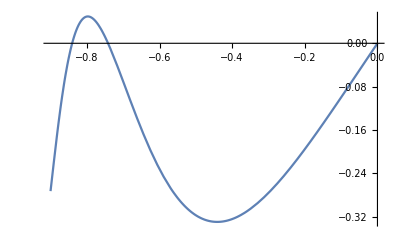

```mathematica
Monitor[Plot[∑_(i=1)^17 1/6 i x^(-1/2-3^i) (x^(3^i/2) (-1+x^(3^i)) (6+6 x^(3^i)+x^(4 3^i))+6 x^(3^i/2) Cosh[x^(3^(1+i)/2)]+6 Sinh[x^(3^(1+i)/2)]),{x,-0.9,0}],{Slider[-x],i}]
```

```mathematica
ExpandNumerator[1/6 i x^(-1/2-3^i) (x^(3^i/2) (-1+x^(3^i)) (6+6 x^(3^i)+x^(4 3^i))+6 x^(3^i/2) Cosh[x^(3^(1+i)/2)]+6 Sinh[x^(3^(1+i)/2)])]
```

1/6 x^(-1/2-3^i) (-6 i x^(3^i/2)-i x^(3^(2+i)/2)+6 i x^(3^i+3^(1+i)/2)+i x^(4 3^i+3^(1+i)/2)+6 i x^(3^i/2) Cosh[x^(3^(1+i)/2)]+6 i Sinh[x^(3^(1+i)/2)])

```mathematica
∫_1^∞ (-i x^(-1/2-3^i/2)+i x^(-1/2+3^(1+i)/2)+1/6 i x^(-1/2+3^(2+i)/2)-1/6 i x^(-1/2-3^i+3^(2+i)/2)+i x^(-1/2-3^i/2) Cosh[x^(3^(1+i)/2)]+i x^(-1/2-3^i) Sinh[x^(3^(1+i)/2)])ⅆi
```

$Aborted

```mathematica
∑_(i=1)^∞ (i x^(-1/2-3^i/2) Cosh[x^(3^(1+i)/2)])
```

∑_(i=1)^∞ i x^(-1/2-3^i/2) Cosh[x^(3^(1+i)/2)]

```mathematica
FullSimplify[(i/(0!) x^(1/2 (-1+3^i)))+(i/(1!) x^(1/4 (-2+2 3^(1+i))))+(i/(2!) x^(1/4 (-2+3^i (-3+(-1)^2+6 2))))+(i/(3!) x^(1/4 (-2+2 3^(2+i))))+(∑_(n=2)^∞ i/((2n)!) x^(1/2 (-1+3^i (-1+6 n))))+(∑_(n=2)^∞ i/((2n+1)!) x^(1/2 (-1+3^i (1+6 n)))),Element[i,Integers]]
```

1/6 i x^(-1/2-3^i) (x^(3^i/2) (-1+x^(3^i)) (6+6 x^(3^i)+x^(4 3^i))+6 x^(3^i/2) Cosh[x^(3^(1+i)/2)]+6 Sinh[x^(3^(1+i)/2)])

```mathematica
FullSimplify[(i x^(1/2 (-1+3^i)))+(i x^(1/4 (-2+2 3^(1+i))))+(i x^(1/4 (-2+3^i (-3+(-1)^2+6 2))))+(i x^(1/4 (-2+2 3^(2+i))))+(∑_(n=2)^∞ i x^(1/2 (-1+3^i (-1+6 n))))+(∑_(n=2)^∞ i x^(1/2 (-1+3^i (1+6 n)))),Element[i,Integers]]
```

(i x^(1/2 (-1+3^i)) (1+x^(2 3^i)+x^(4 3^i)-x^(3^(1+i))) (-1-x^(3^i)+x^(3^(1+i))))/(-1+x^(3^(1+i)))

```mathematica
FullSimplify[1/4 (-2+3^i (-3+(-1)^(2n+1)+6 (2n+1))),Element[n,Integers]]
```

1/2 (-1+3^i (1+6 n))

```mathematica
FullSimplify[1/4 (-2+3^i (-3+(-1)^(2n)+6 (2n))),Element[n,Integers]]
```

1/2 (-1+3^i (-1+6 n))

```mathematica
Piecewise[{{1/4 (-2+3^i (-3+(-1)^n+6 n)), n>3}, {1/4 (-2+2 3^(2+i)), n==3}, {1/4 (-2+3^i (-3+(-1)^2+6 2)), n==2}, {1/4 (-2+2 3^(1+i)), n==1}, {1/4 (-2+2 3^i), n==0}, {1/2 (-1+3^i), True}}]
```

```mathematica
∑_(n=0)^∞ i x^d[i,n];∑_(n=0)^∞ i x^d[i,n]/(n!)
```

```mathematica
∑_(i=1)^∞ (1/6 (3 (-1+3^i) ⅇ^w+3^i (6+6 w+w^3+(-6+9 w) Cosh[w]+9 (-1+w) Sinh[w])))
```

Sum::div: Sum does not converge.

∑_(i=1)^∞ 1/6 (3 (-1+3^i) ⅇ^w+3^i (6+6 w+w^3+(-6+9 w) Cosh[w]+9 (-1+w) Sinh[w]))

```mathematica
∑_(n=0)^∞ Subscript[f, i][n] w^n/(n!)==1/6 (3 (-1+3^i) ⅇ^w+3^i (6+6 w+w^3+(-6+9 w) Cosh[w]+9 (-1+w) Sinh[w]))
```

```mathematica
∑_(n=0)^∞ 3^i aa[n] z^n==3^i
```

```mathematica
∑_(n=0)^∞ ((3^i-1)/2)w^n/(n!)
```

```mathematica
FullSimplify[1/2 (-1+3^i) ⅇ^w+3^i/6 (6+6 w+w^3+(-6+9 w) Cosh[w]+9 (-1+w) Sinh[w])]
```

1/6 (3 (-1+3^i) ⅇ^w+3^i (6+6 w+w^3+(-6+9 w) Cosh[w]+9 (-1+w) Sinh[w]))

```mathematica
Table[FullSimplify[SeriesCoefficient[1/2 (-1+3^i) ⅇ^w+3^i/6 (6+6 w+w^3+(-6+9 w) Cosh[w]+9 (-1+w) Sinh[w]),{w,0,j}]j!],{j,0,10}]
```

{1/2 (-1+3^i),1/2 (-1+3^(1+i)),1/2 (-1+5 3^i),1/2 (-1+3^(2+i)),1/2 (-1+11 3^i),1/2 (-1+13 3^i),1/2 (-1+17 3^i),1/2 (-1+19 3^i),1/2 (-1+23 3^i),1/2 (-1+25 3^i),1/2 (-1+29 3^i)}

```mathematica
∑_(n=0)^∞ ((3^i-1)/2+aa[n])w^n/(n!)==∑_(n=0)^∞ ((3^i-1)/2)w^n/(n!)+∑_(n=0)^∞ (aa[n])w^n/(n!)==1/2 (-1+3^i) ⅇ^w+1/6 (6+6 w+w^3+(-6+9 w) Cosh[w]+9 (-1+w) Sinh[w])
```

```mathematica
1/2 (-1+3^i) ⅇ^w+3^i/6 (6+6 w+w^3+(-6+9 w) Cosh[w]+9 (-1+w) Sinh[w])
```

```mathematica
∑_(n=0)^∞ 3^i aa[n] w^n/(n!)==3^i/6 (6+6 w+w^3+(-6+9 w) Cosh[w]+9 (-1+w) Sinh[w])
```

```mathematica
∑_(n=0)^∞ aa[n] w^n/(n!)==1/6 (6+6 w+w^3+(-6+9 w) Cosh[w]+9 (-1+w) Sinh[w])
```

```mathematica
FullSimplify[(-ⅇ^-w/4-1/4 ⅇ^w (-5+6 w)+1/6 (-6-6 w-w^3))(-1)]
```

1/6 (6+6 w+w^3+(-6+9 w) Cosh[w]+9 (-1+w) Sinh[w])

```mathematica
Table[aa[n],{n,0,10}]
```

{0,1,2,4,5,6,8,9,11,12,14}

```mathematica
FullSimplify[(((z+z^2+z^3-z^5+z^6)/((-1+z)^2 (1+z)))ⅇ^(w/z))/z]
```

```mathematica
Residue[(ⅇ^(w/z) (1+z+z^2-z^4+z^5))/((-1+z)^2 (1+z)),{z,1}]+Residue[(ⅇ^(w/z) (1+z+z^2-z^4+z^5))/((-1+z)^2 (1+z)),{z,-1}]+Residue[(ⅇ^(w/z) (1+z+z^2-z^4+z^5))/((-1+z)^2 (1+z)),{z,∞}]
```

-ⅇ^-w/4-1/4 ⅇ^w (-5+6 w)+1/6 (-6-6 w-w^3)

```mathematica
Table[SeriesCoefficient[(-ⅇ^-w/4-1/4 ⅇ^w (-5+6 w)+1/6 (-6-6 w-w^3))(-1),{w,0,j}]*j!,{j,0,10}]
```

{0,1,2,4,5,6,8,9,11,12,14}

```mathematica
-1/259200*10!
```

-14

```mathematica
1/(2π ⅈ)∫(ⅇ^(w/z) (1+z+z^2-z^4+z^5))/((-1+z)^2 (1+z))ⅆz
```

```mathematica
InverseLaplaceTransform[((1/z^6-1/z^5+1/z^3+1/z^2+1/z) z)/((-1+1/z)^2 (1+1/z)),z,w]
```

ⅇ^-w/4+(7 ⅇ^w)/4+w+(3 ⅇ^w w)/2+DiracDelta[w]

```mathematica
1/(2π ⅈ)∫_□^□ (f[z] ⅇ^(w/z))/z ⅆz
```

```mathematica
1/6 (-6-6 w-w^3)
```

```mathematica
1/(2π ⅈ)∫(((z+z^2+z^3-z^5+z^6)/((-1+z)^2 (1+z)))ⅇ^(w/z))/z ⅆz
```

```mathematica
Residue[(((z+z^2+z^3-z^5+z^6)/((-1+z)^2 (1+z)))ⅇ^(w/z))/z,{z,∞}]
```

1/6 (-6-6 w-w^3)

```mathematica
"The nth position of i in the 4s sequence is:"
Piecewise[{{1/4 (-2+3^i (-3+(-1)^n+6 n)), n==2||n>3}, {1/4 (-2+3^i (1+(-1)^n+6 n)), n==0||n==1||n==3}, {1/2 (-1+3^i), True}}]
```

```mathematica
0,1,2,4,5,7,8,10,11,13,14,16,17,19,20,22,23
```

```mathematica
aa[n_]:=aa[n]=If[n<3,n,If[n<6,n+1,aa[n-2]+3]]
```

```mathematica
FindSequenceFunction[Table[aa[i],{i,0,50}]]
```

DifferenceRoot[Function[{y,n},{4-3 n+y[n]+y[1+n]==0,y[1]==0,y[2]==1,y[3]==2,y[4]==4,y[5]==5}]]

```mathematica
$RecursionLimit=1000000;
```

```mathematica
FindGeneratingFunction[Table[aa[i],{i,0,10000}],z]
```

$Aborted

```mathematica
FindGeneratingFunction[Table[aa[i],{i,0,1000}],z]
```

(z+z^2+z^3-z^5+z^6)/((-1+z)^2 (1+z))

```mathematica
SeriesCoefficient[Out[390],{z,0,n}]
```

Piecewise[{{1/4 (-5+(-1)^n+6 n), n==2||n>3}, {1/4 (-1+(-1)^n+6 n), n==0||n==1||n==3}, {0, True}}]

```mathematica
(3^i-1)/2,(3^i-1)/2+3^i,(3^i-1)/2+3^i+3^i,(3^i-1)/2+3^i+3^i+2*3^i
```

```mathematica
Table[(3^i-1)/2,{i,1,10}]
```

{1,4,13,40,121,364,1093,3280,9841,29524}

```mathematica
Table[take[Flatten[Position[fs,i]],10],{i,1,9}]//Column
```

{1,2,3,5,6,8,9,11,12,14}
{4,7,10,16,19,25,28,34,37,43}
{13,22,31,49,58,76,85,103,112,130}
{40,67,94,148,175,229,256,310,337,391}
{121,202,283,445,526,688,769,931,1012,1174}
{364,607,850,1336,1579,2065,2308,2794,3037,3523}
{1093,1822,2551,4009,4738,6196,6925,8383,9112,10570}
{3280,5467,7654,12028,14215,18589,20776,25150,27337}
{9841,16402,22963}

```mathematica
Differences[Flatten[Position[fs,6]]]
```

{243,243,486,243,486,243,486,243,486,243,486,243,486,243,486,243,486,243,486,243,486,243,486,243,486,243,486,243,486,243,486,243,486,243,486,243,486,243,486,243,486,243,486,243,486,243,486,243,486,243,486,243,486,243,486,243,486,243,486,243,486,243,486,243,486,243,486,243,486,243,486,243,486,243,486,243,486}

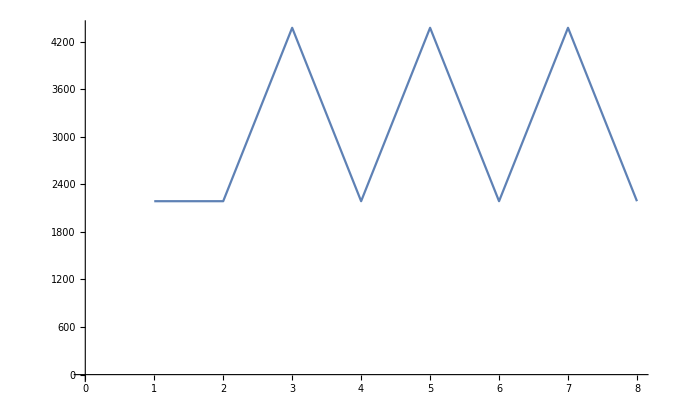

```mathematica
ListPlot[Differences[Flatten[Position[fs,8]]],Joined->True]
```

```mathematica
64/4
```

16

```mathematica
Table[ToExpression[StringJoin["x",ToString[i]]],{i,1,16}]
```

{x1,x2,x3,x4,x5,x6,x7,x8,x9,x10,x11,x12,x13,x14,x15,x16}

```mathematica
xi&&(not x[i-1] || not x[i-2] || not ..)&&xj
```

```mathematica
xi&&not( x[i-1] && x[i-2] && ..)&&xj
```

```mathematica
x[i_]:=ToExpression[StringJoin["x",ToString[i]]]
ij[{i_,j_}]:=x[i]&&((Or@@Table[¬x[k],{k,i+1,j-1}]))&&x[j]
```

```mathematica
ij[{1,4}]
```

x1&&(!x2||!x3)&&x4

```mathematica
¬And@@Table[x[i],{i,1,3}]
```

!(x1&&x2&&x3)

```mathematica
form=BooleanMinimize[¬(Or@@Map[ij,Select[Flatten[Table[{i,j},{i,1,32},{j,1,32}],1],#[[2]]-2≥#[[1]]&]]),"CNF"]
```

(!x1||!x10||x9)&&(!x1||x10||!x11)&&(!x1||x11||!x12)&&(!x1||x12||!x13)&&(!x1||x13||!x14)&&(!x1||x14||!x15)&&(!x1||x15||!x16)&&(!x1||x16||!x17)&&(!x1||x17||!x18)&&(!x1||x18||!x19)&&(!x1||x19||!x20)&&(!x1||x2||!x3)&&(!x1||x20||!x21)&&(!x1||x21||!x22)&&(!x1||x22||!x23)&&(!x1||x23||!x24)&&(!x1||x24||!x25)&&(!x1||x25||!x26)&&(!x1||x26||!x27)&&(!x1||x27||!x28)&&(!x1||x28||!x29)&&(!x1||x29||!x30)&&(!x1||x3||!x4)&&(!x1||x30||!x31)&&(!x1||x31||!x32)&&(!x1||x4||!x5)&&(!x1||x5||!x6)&&(!x1||x6||!x7)&&(!x1||x7||!x8)&&(!x1||x8||!x9)&&(!x10||x11||!x12)&&(!x10||x12||!x13)&&(!x10||x13||!x14)&&(!x10||x14||!x15)&&(!x10||x15||!x16)&&(!x10||x16||!x17)&&(!x10||x17||!x18)&&(!x10||x18||!x19)&&(!x10||x19||!x20)&&(!x10||!x2||x9)&&(!x10||x20||!x21)&&(!x10||x21||!x22)&&(!x10||x22||!x23)&&(!x10||x23||!x24)&&(!x10||x24||!x25)&&(!x10||x25||!x26)&&(!x10||x26||!x27)&&(!x10||x27||!x28)&&(!x10||x28||!x29)&&(!x10||x29||!x30)&&(!x10||!x3||x9)&&(!x10||x30||!x31)&&(!x10||x31||!x32)&&(!x10||!x4||x9)&&(!x10||!x5||x9)&&(!x10||!x6||x9)&&(!x10||!x7||x9)&&(!x10||!x8||x9)&&(x10||!x11||!x2)&&(x10||!x11||!x3)&&(x10||!x11||!x4)&&(x10||!x11||!x5)&&(x10||!x11||!x6)&&(x10||!x11||!x7)&&(x10||!x11||!x8)&&(x10||!x11||!x9)&&(!x11||x12||!x13)&&(!x11||x13||!x14)&&(!x11||x14||!x15)&&(!x11||x15||!x16)&&(!x11||x16||!x17)&&(!x11||x17||!x18)&&(!x11||x18||!x19)&&(!x11||x19||!x20)&&(!x11||x20||!x21)&&(!x11||x21||!x22)&&(!x11||x22||!x23)&&(!x11||x23||!x24)&&(!x11||x24||!x25)&&(!x11||x25||!x26)&&(!x11||x26||!x27)&&(!x11||x27||!x28)&&(!x11||x28||!x29)&&(!x11||x29||!x30)&&(!x11||x30||!x31)&&(!x11||x31||!x32)&&(x11||!x12||!x2)&&(x11||!x12||!x3)&&(x11||!x12||!x4)&&(x11||!x12||!x5)&&(x11||!x12||!x6)&&(x11||!x12||!x7)&&(x11||!x12||!x8)&&(x11||!x12||!x9)&&(!x12||x13||!x14)&&(!x12||x14||!x15)&&(!x12||x15||!x16)&&(!x12||x16||!x17)&&(!x12||x17||!x18)&&(!x12||x18||!x19)&&(!x12||x19||!x20)&&(!x12||x20||!x21)&&(!x12||x21||!x22)&&(!x12||x22||!x23)&&(!x12||x23||!x24)&&(!x12||x24||!x25)&&(!x12||x25||!x26)&&(!x12||x26||!x27)&&(!x12||x27||!x28)&&(!x12||x28||!x29)&&(!x12||x29||!x30)&&(!x12||x30||!x31)&&(!x12||x31||!x32)&&(x12||!x13||!x2)&&(x12||!x13||!x3)&&(x12||!x13||!x4)&&(x12||!x13||!x5)&&(x12||!x13||!x6)&&(x12||!x13||!x7)&&(x12||!x13||!x8)&&(x12||!x13||!x9)&&(!x13||x14||!x15)&&(!x13||x15||!x16)&&(!x13||x16||!x17)&&(!x13||x17||!x18)&&(!x13||x18||!x19)&&(!x13||x19||!x20)&&(!x13||x20||!x21)&&(!x13||x21||!x22)&&(!x13||x22||!x23)&&(!x13||x23||!x24)&&(!x13||x24||!x25)&&(!x13||x25||!x26)&&(!x13||x26||!x27)&&(!x13||x27||!x28)&&(!x13||x28||!x29)&&(!x13||x29||!x30)&&(!x13||x30||!x31)&&(!x13||x31||!x32)&&(x13||!x14||!x2)&&(x13||!x14||!x3)&&(x13||!x14||!x4)&&(x13||!x14||!x5)&&(x13||!x14||!x6)&&(x13||!x14||!x7)&&(x13||!x14||!x8)&&(x13||!x14||!x9)&&(!x14||x15||!x16)&&(!x14||x16||!x17)&&(!x14||x17||!x18)&&(!x14||x18||!x19)&&(!x14||x19||!x20)&&(!x14||x20||!x21)&&(!x14||x21||!x22)&&(!x14||x22||!x23)&&(!x14||x23||!x24)&&(!x14||x24||!x25)&&(!x14||x25||!x26)&&(!x14||x26||!x27)&&(!x14||x27||!x28)&&(!x14||x28||!x29)&&(!x14||x29||!x30)&&(!x14||x30||!x31)&&(!x14||x31||!x32)&&(x14||!x15||!x2)&&(x14||!x15||!x3)&&(x14||!x15||!x4)&&(x14||!x15||!x5)&&(x14||!x15||!x6)&&(x14||!x15||!x7)&&(x14||!x15||!x8)&&(x14||!x15||!x9)&&(!x15||x16||!x17)&&(!x15||x17||!x18)&&(!x15||x18||!x19)&&(!x15||x19||!x20)&&(!x15||x20||!x21)&&(!x15||x21||!x22)&&(!x15||x22||!x23)&&(!x15||x23||!x24)&&(!x15||x24||!x25)&&(!x15||x25||!x26)&&(!x15||x26||!x27)&&(!x15||x27||!x28)&&(!x15||x28||!x29)&&(!x15||x29||!x30)&&(!x15||x30||!x31)&&(!x15||x31||!x32)&&(x15||!x16||!x2)&&(x15||!x16||!x3)&&(x15||!x16||!x4)&&(x15||!x16||!x5)&&(x15||!x16||!x6)&&(x15||!x16||!x7)&&(x15||!x16||!x8)&&(x15||!x16||!x9)&&(!x16||x17||!x18)&&(!x16||x18||!x19)&&(!x16||x19||!x20)&&(!x16||x20||!x21)&&(!x16||x21||!x22)&&(!x16||x22||!x23)&&(!x16||x23||!x24)&&(!x16||x24||!x25)&&(!x16||x25||!x26)&&(!x16||x26||!x27)&&(!x16||x27||!x28)&&(!x16||x28||!x29)&&(!x16||x29||!x30)&&(!x16||x30||!x31)&&(!x16||x31||!x32)&&(x16||!x17||!x2)&&(x16||!x17||!x3)&&(x16||!x17||!x4)&&(x16||!x17||!x5)&&(x16||!x17||!x6)&&(x16||!x17||!x7)&&(x16||!x17||!x8)&&(x16||!x17||!x9)&&(!x17||x18||!x19)&&(!x17||x19||!x20)&&(!x17||x20||!x21)&&(!x17||x21||!x22)&&(!x17||x22||!x23)&&(!x17||x23||!x24)&&(!x17||x24||!x25)&&(!x17||x25||!x26)&&(!x17||x26||!x27)&&(!x17||x27||!x28)&&(!x17||x28||!x29)&&(!x17||x29||!x30)&&(!x17||x30||!x31)&&(!x17||x31||!x32)&&(x17||!x18||!x2)&&(x17||!x18||!x3)&&(x17||!x18||!x4)&&(x17||!x18||!x5)&&(x17||!x18||!x6)&&(x17||!x18||!x7)&&(x17||!x18||!x8)&&(x17||!x18||!x9)&&(!x18||x19||!x20)&&(!x18||x20||!x21)&&(!x18||x21||!x22)&&(!x18||x22||!x23)&&(!x18||x23||!x24)&&(!x18||x24||!x25)&&(!x18||x25||!x26)&&(!x18||x26||!x27)&&(!x18||x27||!x28)&&(!x18||x28||!x29)&&(!x18||x29||!x30)&&(!x18||x30||!x31)&&(!x18||x31||!x32)&&(x18||!x19||!x2)&&(x18||!x19||!x3)&&(x18||!x19||!x4)&&(x18||!x19||!x5)&&(x18||!x19||!x6)&&(x18||!x19||!x7)&&(x18||!x19||!x8)&&(x18||!x19||!x9)&&(!x19||x20||!x21)&&(!x19||x21||!x22)&&(!x19||x22||!x23)&&(!x19||x23||!x24)&&(!x19||x24||!x25)&&(!x19||x25||!x26)&&(!x19||x26||!x27)&&(!x19||x27||!x28)&&(!x19||x28||!x29)&&(!x19||x29||!x30)&&(!x19||x30||!x31)&&(!x19||x31||!x32)&&(x19||!x2||!x20)&&(x19||!x20||!x3)&&(x19||!x20||!x4)&&(x19||!x20||!x5)&&(x19||!x20||!x6)&&(x19||!x20||!x7)&&(x19||!x20||!x8)&&(x19||!x20||!x9)&&(!x2||x20||!x21)&&(!x2||x21||!x22)&&(!x2||x22||!x23)&&(!x2||x23||!x24)&&(!x2||x24||!x25)&&(!x2||x25||!x26)&&(!x2||x26||!x27)&&(!x2||x27||!x28)&&(!x2||x28||!x29)&&(!x2||x29||!x30)&&(!x2||x3||!x4)&&(!x2||x30||!x31)&&(!x2||x31||!x32)&&(!x2||x4||!x5)&&(!x2||x5||!x6)&&(!x2||x6||!x7)&&(!x2||x7||!x8)&&(!x2||x8||!x9)&&(!x20||x21||!x22)&&(!x20||x22||!x23)&&(!x20||x23||!x24)&&(!x20||x24||!x25)&&(!x20||x25||!x26)&&(!x20||x26||!x27)&&(!x20||x27||!x28)&&(!x20||x28||!x29)&&(!x20||x29||!x30)&&(!x20||x30||!x31)&&(!x20||x31||!x32)&&(x20||!x21||!x3)&&(x20||!x21||!x4)&&(x20||!x21||!x5)&&(x20||!x21||!x6)&&(x20||!x21||!x7)&&(x20||!x21||!x8)&&(x20||!x21||!x9)&&(!x21||x22||!x23)&&(!x21||x23||!x24)&&(!x21||x24||!x25)&&(!x21||x25||!x26)&&(!x21||x26||!x27)&&(!x21||x27||!x28)&&(!x21||x28||!x29)&&(!x21||x29||!x30)&&(!x21||x30||!x31)&&(!x21||x31||!x32)&&(x21||!x22||!x3)&&(x21||!x22||!x4)&&(x21||!x22||!x5)&&(x21||!x22||!x6)&&(x21||!x22||!x7)&&(x21||!x22||!x8)&&(x21||!x22||!x9)&&(!x22||x23||!x24)&&(!x22||x24||!x25)&&(!x22||x25||!x26)&&(!x22||x26||!x27)&&(!x22||x27||!x28)&&(!x22||x28||!x29)&&(!x22||x29||!x30)&&(!x22||x30||!x31)&&(!x22||x31||!x32)&&(x22||!x23||!x3)&&(x22||!x23||!x4)&&(x22||!x23||!x5)&&(x22||!x23||!x6)&&(x22||!x23||!x7)&&(x22||!x23||!x8)&&(x22||!x23||!x9)&&(!x23||x24||!x25)&&(!x23||x25||!x26)&&(!x23||x26||!x27)&&(!x23||x27||!x28)&&(!x23||x28||!x29)&&(!x23||x29||!x30)&&(!x23||x30||!x31)&&(!x23||x31||!x32)&&(x23||!x24||!x3)&&(x23||!x24||!x4)&&(x23||!x24||!x5)&&(x23||!x24||!x6)&&(x23||!x24||!x7)&&(x23||!x24||!x8)&&(x23||!x24||!x9)&&(!x24||x25||!x26)&&(!x24||x26||!x27)&&(!x24||x27||!x28)&&(!x24||x28||!x29)&&(!x24||x29||!x30)&&(!x24||x30||!x31)&&(!x24||x31||!x32)&&(x24||!x25||!x3)&&(x24||!x25||!x4)&&(x24||!x25||!x5)&&(x24||!x25||!x6)&&(x24||!x25||!x7)&&(x24||!x25||!x8)&&(x24||!x25||!x9)&&(!x25||x26||!x27)&&(!x25||x27||!x28)&&(!x25||x28||!x29)&&(!x25||x29||!x30)&&(!x25||x30||!x31)&&(!x25||x31||!x32)&&(x25||!x26||!x3)&&(x25||!x26||!x4)&&(x25||!x26||!x5)&&(x25||!x26||!x6)&&(x25||!x26||!x7)&&(x25||!x26||!x8)&&(x25||!x26||!x9)&&(!x26||x27||!x28)&&(!x26||x28||!x29)&&(!x26||x29||!x30)&&(!x26||x30||!x31)&&(!x26||x31||!x32)&&(x26||!x27||!x3)&&(x26||!x27||!x4)&&(x26||!x27||!x5)&&(x26||!x27||!x6)&&(x26||!x27||!x7)&&(x26||!x27||!x8)&&(x26||!x27||!x9)&&(!x27||x28||!x29)&&(!x27||x29||!x30)&&(!x27||x30||!x31)&&(!x27||x31||!x32)&&(x27||!x28||!x3)&&(x27||!x28||!x4)&&(x27||!x28||!x5)&&(x27||!x28||!x6)&&(x27||!x28||!x7)&&(x27||!x28||!x8)&&(x27||!x28||!x9)&&(!x28||x29||!x30)&&(!x28||x30||!x31)&&(!x28||x31||!x32)&&(x28||!x29||!x3)&&(x28||!x29||!x4)&&(x28||!x29||!x5)&&(x28||!x29||!x6)&&(x28||!x29||!x7)&&(x28||!x29||!x8)&&(x28||!x29||!x9)&&(!x29||x30||!x31)&&(!x29||x31||!x32)&&(x29||!x3||!x30)&&(x29||!x30||!x4)&&(x29||!x30||!x5)&&(x29||!x30||!x6)&&(x29||!x30||!x7)&&(x29||!x30||!x8)&&(x29||!x30||!x9)&&(!x3||x30||!x31)&&(!x3||x31||!x32)&&(!x3||x4||!x5)&&(!x3||x5||!x6)&&(!x3||x6||!x7)&&(!x3||x7||!x8)&&(!x3||x8||!x9)&&(!x30||x31||!x32)&&(x30||!x31||!x4)&&(x30||!x31||!x5)&&(x30||!x31||!x6)&&(x30||!x31||!x7)&&(x30||!x31||!x8)&&(x30||!x31||!x9)&&(x31||!x32||!x4)&&(x31||!x32||!x5)&&(x31||!x32||!x6)&&(x31||!x32||!x7)&&(x31||!x32||!x8)&&(x31||!x32||!x9)&&(!x4||x5||!x6)&&(!x4||x6||!x7)&&(!x4||x7||!x8)&&(!x4||x8||!x9)&&(!x5||x6||!x7)&&(!x5||x7||!x8)&&(!x5||x8||!x9)&&(!x6||x7||!x8)&&(!x6||x8||!x9)&&(!x7||x8||!x9)

```mathematica
gd[5]
try[5]
```

True

False

```mathematica
InterpolatingPolynomial[{{0,0},{15,60}},a]
```

4 a

```mathematica
try[z_]:=form/.Table[x[i]->(PadLeft[IntegerDigits[z,2],32][[i]]==1),{i,1,32}]
```

```mathematica
rep[s_]:=StringJoin["x",ToString[(ToExpression[StringDrop[s,1]]-1)]]
```

```mathematica
rep["x11"]
```

x10

```mathematica
StringReplace[ToString[form],{"!"->"n ",a:RegularExpression["x\\d+"]:>rep[a]," "->""}]
```

(n x0||n x9||x8)&&(n x0||x9||n x10)&&(n x0||x10||n x11)&&(n x0||x11||n x12)&&(n x0||x12||n x13)&&(n x0||x13||n x14)&&(n x0||x14||n x15)&&(n x0||x15||n x16)&&(n x0||x16||n x17)&&(n x0||x17||n x18)&&(n x0||x18||n x19)&&(n x0||x1||n x2)&&(n x0||x19||n x20)&&(n x0||x20||n x21)&&(n x0||x21||n x22)&&(n x0||x22||n x23)&&(n x0||x23||n x24)&&(n x0||x24||n x25)&&(n x0||x25||n x26)&&(n x0||x26||n x27)&&(n x0||x27||n x28)&&(n x0||x28||n x29)&&(n x0||x2||n x3)&&(n x0||x29||n x30)&&(n x0||x30||n x31)&&(n x0||x3||n x4)&&(n x0||x4||n x5)&&(n x0||x5||n x6)&&(n x0||x6||n x7)&&(n x0||x7||n x8)&&(n x9||x10||n x11)&&(n x9||x11||n x12)&&(n x9||x12||n x13)&&(n x9||x13||n x14)&&(n x9||x14||n x15)&&(n x9||x15||n x16)&&(n x9||x16||n x17)&&(n x9||x17||n x18)&&(n x9||x18||n x19)&&(n x9||n x1||x8)&&(n x9||x19||n x20)&&(n x9||x20||n x21)&&(n x9||x21||n x22)&&(n x9||x22||n x23)&&(n x9||x23||n x24)&&(n x9||x24||n x25)&&(n x9||x25||n x26)&&(n x9||x26||n x27)&&(n x9||x27||n x28)&&(n x9||x28||n x29)&&(n x9||n x2||x8)&&(n x9||x29||n x30)&&(n x9||x30||n x31)&&(n x9||n x3||x8)&&(n x9||n x4||x8)&&(n x9||n x5||x8)&&(n x9||n x6||x8)&&(n x9||n x7||x8)&&(x9||n x10||n x1)&&(x9||n x10||n x2)&&(x9||n x10||n x3)&&(x9||n x10||n x4)&&(x9||n x10||n x5)&&(x9||n x10||n x6)&&(x9||n x10||n x7)&&(x9||n x10||n x8)&&(n x10||x11||n x12)&&(n x10||x12||n x13)&&(n x10||x13||n x14)&&(n x10||x14||n x15)&&(n x10||x15||n x16)&&(n x10||x16||n x17)&&(n x10||x17||n x18)&&(n x10||x18||n x19)&&(n x10||x19||n x20)&&(n x10||x20||n x21)&&(n x10||x21||n x22)&&(n x10||x22||n x23)&&(n x10||x23||n x24)&&(n x10||x24||n x25)&&(n x10||x25||n x26)&&(n x10||x26||n x27)&&(n x10||x27||n x28)&&(n x10||x28||n x29)&&(n x10||x29||n x30)&&(n x10||x30||n x31)&&(x10||n x11||n x1)&&(x10||n x11||n x2)&&(x10||n x11||n x3)&&(x10||n x11||n x4)&&(x10||n x11||n x5)&&(x10||n x11||n x6)&&(x10||n x11||n x7)&&(x10||n x11||n x8)&&(n x11||x12||n x13)&&(n x11||x13||n x14)&&(n x11||x14||n x15)&&(n x11||x15||n x16)&&(n x11||x16||n x17)&&(n x11||x17||n x18)&&(n x11||x18||n x19)&&(n x11||x19||n x20)&&(n x11||x20||n x21)&&(n x11||x21||n x22)&&(n x11||x22||n x23)&&(n x11||x23||n x24)&&(n x11||x24||n x25)&&(n x11||x25||n x26)&&(n x11||x26||n x27)&&(n x11||x27||n x28)&&(n x11||x28||n x29)&&(n x11||x29||n x30)&&(n x11||x30||n x31)&&(x11||n x12||n x1)&&(x11||n x12||n x2)&&(x11||n x12||n x3)&&(x11||n x12||n x4)&&(x11||n x12||n x5)&&(x11||n x12||n x6)&&(x11||n x12||n x7)&&(x11||n x12||n x8)&&(n x12||x13||n x14)&&(n x12||x14||n x15)&&(n x12||x15||n x16)&&(n x12||x16||n x17)&&(n x12||x17||n x18)&&(n x12||x18||n x19)&&(n x12||x19||n x20)&&(n x12||x20||n x21)&&(n x12||x21||n x22)&&(n x12||x22||n x23)&&(n x12||x23||n x24)&&(n x12||x24||n x25)&&(n x12||x25||n x26)&&(n x12||x26||n x27)&&(n x12||x27||n x28)&&(n x12||x28||n x29)&&(n x12||x29||n x30)&&(n x12||x30||n x31)&&(x12||n x13||n x1)&&(x12||n x13||n x2)&&(x12||n x13||n x3)&&(x12||n x13||n x4)&&(x12||n x13||n x5)&&(x12||n x13||n x6)&&(x12||n x13||n x7)&&(x12||n x13||n x8)&&(n x13||x14||n x15)&&(n x13||x15||n x16)&&(n x13||x16||n x17)&&(n x13||x17||n x18)&&(n x13||x18||n x19)&&(n x13||x19||n x20)&&(n x13||x20||n x21)&&(n x13||x21||n x22)&&(n x13||x22||n x23)&&(n x13||x23||n x24)&&(n x13||x24||n x25)&&(n x13||x25||n x26)&&(n x13||x26||n x27)&&(n x13||x27||n x28)&&(n x13||x28||n x29)&&(n x13||x29||n x30)&&(n x13||x30||n x31)&&(x13||n x14||n x1)&&(x13||n x14||n x2)&&(x13||n x14||n x3)&&(x13||n x14||n x4)&&(x13||n x14||n x5)&&(x13||n x14||n x6)&&(x13||n x14||n x7)&&(x13||n x14||n x8)&&(n x14||x15||n x16)&&(n x14||x16||n x17)&&(n x14||x17||n x18)&&(n x14||x18||n x19)&&(n x14||x19||n x20)&&(n x14||x20||n x21)&&(n x14||x21||n x22)&&(n x14||x22||n x23)&&(n x14||x23||n x24)&&(n x14||x24||n x25)&&(n x14||x25||n x26)&&(n x14||x26||n x27)&&(n x14||x27||n x28)&&(n x14||x28||n x29)&&(n x14||x29||n x30)&&(n x14||x30||n x31)&&(x14||n x15||n x1)&&(x14||n x15||n x2)&&(x14||n x15||n x3)&&(x14||n x15||n x4)&&(x14||n x15||n x5)&&(x14||n x15||n x6)&&(x14||n x15||n x7)&&(x14||n x15||n x8)&&(n x15||x16||n x17)&&(n x15||x17||n x18)&&(n x15||x18||n x19)&&(n x15||x19||n x20)&&(n x15||x20||n x21)&&(n x15||x21||n x22)&&(n x15||x22||n x23)&&(n x15||x23||n x24)&&(n x15||x24||n x25)&&(n x15||x25||n x26)&&(n x15||x26||n x27)&&(n x15||x27||n x28)&&(n x15||x28||n x29)&&(n x15||x29||n x30)&&(n x15||x30||n x31)&&(x15||n x16||n x1)&&(x15||n x16||n x2)&&(x15||n x16||n x3)&&(x15||n x16||n x4)&&(x15||n x16||n x5)&&(x15||n x16||n x6)&&(x15||n x16||n x7)&&(x15||n x16||n x8)&&(n x16||x17||n x18)&&(n x16||x18||n x19)&&(n x16||x19||n x20)&&(n x16||x20||n x21)&&(n x16||x21||n x22)&&(n x16||x22||n x23)&&(n x16||x23||n x24)&&(n x16||x24||n x25)&&(n x16||x25||n x26)&&(n x16||x26||n x27)&&(n x16||x27||n x28)&&(n x16||x28||n x29)&&(n x16||x29||n x30)&&(n x16||x30||n x31)&&(x16||n x17||n x1)&&(x16||n x17||n x2)&&(x16||n x17||n x3)&&(x16||n x17||n x4)&&(x16||n x17||n x5)&&(x16||n x17||n x6)&&(x16||n x17||n x7)&&(x16||n x17||n x8)&&(n x17||x18||n x19)&&(n x17||x19||n x20)&&(n x17||x20||n x21)&&(n x17||x21||n x22)&&(n x17||x22||n x23)&&(n x17||x23||n x24)&&(n x17||x24||n x25)&&(n x17||x25||n x26)&&(n x17||x26||n x27)&&(n x17||x27||n x28)&&(n x17||x28||n x29)&&(n x17||x29||n x30)&&(n x17||x30||n x31)&&(x17||n x18||n x1)&&(x17||n x18||n x2)&&(x17||n x18||n x3)&&(x17||n x18||n x4)&&(x17||n x18||n x5)&&(x17||n x18||n x6)&&(x17||n x18||n x7)&&(x17||n x18||n x8)&&(n x18||x19||n x20)&&(n x18||x20||n x21)&&(n x18||x21||n x22)&&(n x18||x22||n x23)&&(n x18||x23||n x24)&&(n x18||x24||n x25)&&(n x18||x25||n x26)&&(n x18||x26||n x27)&&(n x18||x27||n x28)&&(n x18||x28||n x29)&&(n x18||x29||n x30)&&(n x18||x30||n x31)&&(x18||n x1||n x19)&&(x18||n x19||n x2)&&(x18||n x19||n x3)&&(x18||n x19||n x4)&&(x18||n x19||n x5)&&(x18||n x19||n x6)&&(x18||n x19||n x7)&&(x18||n x19||n x8)&&(n x1||x19||n x20)&&(n x1||x20||n x21)&&(n x1||x21||n x22)&&(n x1||x22||n x23)&&(n x1||x23||n x24)&&(n x1||x24||n x25)&&(n x1||x25||n x26)&&(n x1||x26||n x27)&&(n x1||x27||n x28)&&(n x1||x28||n x29)&&(n x1||x2||n x3)&&(n x1||x29||n x30)&&(n x1||x30||n x31)&&(n x1||x3||n x4)&&(n x1||x4||n x5)&&(n x1||x5||n x6)&&(n x1||x6||n x7)&&(n x1||x7||n x8)&&(n x19||x20||n x21)&&(n x19||x21||n x22)&&(n x19||x22||n x23)&&(n x19||x23||n x24)&&(n x19||x24||n x25)&&(n x19||x25||n x26)&&(n x19||x26||n x27)&&(n x19||x27||n x28)&&(n x19||x28||n x29)&&(n x19||x29||n x30)&&(n x19||x30||n x31)&&(x19||n x20||n x2)&&(x19||n x20||n x3)&&(x19||n x20||n x4)&&(x19||n x20||n x5)&&(x19||n x20||n x6)&&(x19||n x20||n x7)&&(x19||n x20||n x8)&&(n x20||x21||n x22)&&(n x20||x22||n x23)&&(n x20||x23||n x24)&&(n x20||x24||n x25)&&(n x20||x25||n x26)&&(n x20||x26||n x27)&&(n x20||x27||n x28)&&(n x20||x28||n x29)&&(n x20||x29||n x30)&&(n x20||x30||n x31)&&(x20||n x21||n x2)&&(x20||n x21||n x3)&&(x20||n x21||n x4)&&(x20||n x21||n x5)&&(x20||n x21||n x6)&&(x20||n x21||n x7)&&(x20||n x21||n x8)&&(n x21||x22||n x23)&&(n x21||x23||n x24)&&(n x21||x24||n x25)&&(n x21||x25||n x26)&&(n x21||x26||n x27)&&(n x21||x27||n x28)&&(n x21||x28||n x29)&&(n x21||x29||n x30)&&(n x21||x30||n x31)&&(x21||n x22||n x2)&&(x21||n x22||n x3)&&(x21||n x22||n x4)&&(x21||n x22||n x5)&&(x21||n x22||n x6)&&(x21||n x22||n x7)&&(x21||n x22||n x8)&&(n x22||x23||n x24)&&(n x22||x24||n x25)&&(n x22||x25||n x26)&&(n x22||x26||n x27)&&(n x22||x27||n x28)&&(n x22||x28||n x29)&&(n x22||x29||n x30)&&(n x22||x30||n x31)&&(x22||n x23||n x2)&&(x22||n x23||n x3)&&(x22||n x23||n x4)&&(x22||n x23||n x5)&&(x22||n x23||n x6)&&(x22||n x23||n x7)&&(x22||n x23||n x8)&&(n x23||x24||n x25)&&(n x23||x25||n x26)&&(n x23||x26||n x27)&&(n x23||x27||n x28)&&(n x23||x28||n x29)&&(n x23||x29||n x30)&&(n x23||x30||n x31)&&(x23||n x24||n x2)&&(x23||n x24||n x3)&&(x23||n x24||n x4)&&(x23||n x24||n x5)&&(x23||n x24||n x6)&&(x23||n x24||n x7)&&(x23||n x24||n x8)&&(n x24||x25||n x26)&&(n x24||x26||n x27)&&(n x24||x27||n x28)&&(n x24||x28||n x29)&&(n x24||x29||n x30)&&(n x24||x30||n x31)&&(x24||n x25||n x2)&&(x24||n x25||n x3)&&(x24||n x25||n x4)&&(x24||n x25||n x5)&&(x24||n x25||n x6)&&(x24||n x25||n x7)&&(x24||n x25||n x8)&&(n x25||x26||n x27)&&(n x25||x27||n x28)&&(n x25||x28||n x29)&&(n x25||x29||n x30)&&(n x25||x30||n x31)&&(x25||n x26||n x2)&&(x25||n x26||n x3)&&(x25||n x26||n x4)&&(x25||n x26||n x5)&&(x25||n x26||n x6)&&(x25||n x26||n x7)&&(x25||n x26||n x8)&&(n x26||x27||n x28)&&(n x26||x28||n x29)&&(n x26||x29||n x30)&&(n x26||x30||n x31)&&(x26||n x27||n x2)&&(x26||n x27||n x3)&&(x26||n x27||n x4)&&(x26||n x27||n x5)&&(x26||n x27||n x6)&&(x26||n x27||n x7)&&(x26||n x27||n x8)&&(n x27||x28||n x29)&&(n x27||x29||n x30)&&(n x27||x30||n x31)&&(x27||n x28||n x2)&&(x27||n x28||n x3)&&(x27||n x28||n x4)&&(x27||n x28||n x5)&&(x27||n x28||n x6)&&(x27||n x28||n x7)&&(x27||n x28||n x8)&&(n x28||x29||n x30)&&(n x28||x30||n x31)&&(x28||n x2||n x29)&&(x28||n x29||n x3)&&(x28||n x29||n x4)&&(x28||n x29||n x5)&&(x28||n x29||n x6)&&(x28||n x29||n x7)&&(x28||n x29||n x8)&&(n x2||x29||n x30)&&(n x2||x30||n x31)&&(n x2||x3||n x4)&&(n x2||x4||n x5)&&(n x2||x5||n x6)&&(n x2||x6||n x7)&&(n x2||x7||n x8)&&(n x29||x30||n x31)&&(x29||n x30||n x3)&&(x29||n x30||n x4)&&(x29||n x30||n x5)&&(x29||n x30||n x6)&&(x29||n x30||n x7)&&(x29||n x30||n x8)&&(x30||n x31||n x3)&&(x30||n x31||n x4)&&(x30||n x31||n x5)&&(x30||n x31||n x6)&&(x30||n x31||n x7)&&(x30||n x31||n x8)&&(n x3||x4||n x5)&&(n x3||x5||n x6)&&(n x3||x6||n x7)&&(n x3||x7||n x8)&&(n x4||x5||n x6)&&(n x4||x6||n x7)&&(n x4||x7||n x8)&&(n x5||x6||n x7)&&(n x5||x7||n x8)&&(n x6||x7||n x8)

```mathematica
Table[ToString[x[i]],{i,1,20}]
```

{x1,x2,x3,x4,x5,x6,x7,x8,x9,x10,x11,x12,x13,x14,x15,x16,x17,x18,x19,x20}

```mathematica
StringReplace["|| not x10 || x9) && (not x1 || x10 || not x11) && (not x1 || x11 || not x12) && (not x1 || x12 || not x13) && (not x1 || x13 || not x14) && (not x1 || x14 || not x15) && (not x1 || x15 || not x16) && (not x1 || x2 || not x3) && (not x1 || x3 || not x4) && (not x1 || x4 || not x5) && (not x1 || x5 || not x6) && (not x1 || x6 || not x7) && (not x1 || x7 || not x8) && (not x1 || x8 || not x9) && (not x10 || x11 || not x12) && (not x10 || x12 || not x13) && (not x10 || x13 || not x14) && (not x10 || x14 || not x15) && (not x10 || x15 || not x16) && (not x10 || not x2 || x9) && (not x10 || not x3 || x9) && (not x10 || not x4 || x9) && (not x10 || not x5 || x9) && (not x10 || not x6 || x9) && (not x10 || not x7 || x9) && (not x10 || not x8 || x9) && (x10 || not x11 || not x2) && (x10 || not x11 || not x3) && (x10 || not x11 || not x4) && (x10 || not x11 || not x5) && (x10 || not x11 || not x6)"
```

|| not (testBit z 9) || (testBit z 8)) && (not (testBit z 0) || (testBit z 9) || not (testBit z 10)) && (not (testBit z 0) || (testBit z 10) || not (testBit z 11)) && (not (testBit z 0) || (testBit z 11) || not (testBit z 12)) && (not (testBit z 0) || (testBit z 12) || not (testBit z 13)) && (not (testBit z 0) || (testBit z 13) || not (testBit z 14)) && (not (testBit z 0) || (testBit z 14) || not (testBit z 15)) && (not (testBit z 0) || (testBit z 1) || not (testBit z 2)) && (not (testBit z 0) || (testBit z 2) || not (testBit z 3)) && (not (testBit z 0) || (testBit z 3) || not (testBit z 4)) && (not (testBit z 0) || (testBit z 4) || not (testBit z 5)) && (not (testBit z 0) || (testBit z 5) || not (testBit z 6)) && (not (testBit z 0) || (testBit z 6) || not (testBit z 7)) && (not (testBit z 0) || (testBit z 7) || not (testBit z 8)) && (not (testBit z 9) || (testBit z 10) || not (testBit z 11)) && (not (testBit z 9) || (testBit z 11) || not (testBit z 12)) && (not (testBit z 9) || (testBit z 12) || not (testBit z 13)) && (not (testBit z 9) || (testBit z 13) || not (testBit z 14)) && (not (testBit z 9) || (testBit z 14) || not (testBit z 15)) && (not (testBit z 9) || not (testBit z 1) || (testBit z 8)) && (not (testBit z 9) || not (testBit z 2) || (testBit z 8)) && (not (testBit z 9) || not (testBit z 3) || (testBit z 8)) && (not (testBit z 9) || not (testBit z 4) || (testBit z 8)) && (not (testBit z 9) || not (testBit z 5) || (testBit z 8)) && (not (testBit z 9) || not (testBit z 6) || (testBit z 8)) && (not (testBit z 9) || not (testBit z 7) || (testBit z 8)) && ((testBit z 9) || not (testBit z 10) || not (testBit z 1)) && ((testBit z 9) || not (testBit z 10) || not (testBit z 2)) && ((testBit z 9) || not (testBit z 10) || not (testBit z 3)) && ((testBit z 9) || not (testBit z 10) || not (testBit z 4)) && ((testBit z 9) || not (testBit z 10) || not (testBit z 5))

```mathematica
StringJoin[Table[StringJoin["    z",ToString[i]," = unsafeShiftR z",ToString[i-1]," 2\n"],{i,1,31}]]
```

z1 = unsafeShiftR z0 2
    z2 = unsafeShiftR z1 2
    z3 = unsafeShiftR z2 2
    z4 = unsafeShiftR z3 2
    z5 = unsafeShiftR z4 2
    z6 = unsafeShiftR z5 2
    z7 = unsafeShiftR z6 2
    z8 = unsafeShiftR z7 2
    z9 = unsafeShiftR z8 2
    z10 = unsafeShiftR z9 2
    z11 = unsafeShiftR z10 2
    z12 = unsafeShiftR z11 2
    z13 = unsafeShiftR z12 2
    z14 = unsafeShiftR z13 2
    z15 = unsafeShiftR z14 2
    z16 = unsafeShiftR z15 2
    z17 = unsafeShiftR z16 2
    z18 = unsafeShiftR z17 2
    z19 = unsafeShiftR z18 2
    z20 = unsafeShiftR z19 2
    z21 = unsafeShiftR z20 2
    z22 = unsafeShiftR z21 2
    z23 = unsafeShiftR z22 2
    z24 = unsafeShiftR z23 2
    z25 = unsafeShiftR z24 2
    z26 = unsafeShiftR z25 2
    z27 = unsafeShiftR z26 2
    z28 = unsafeShiftR z27 2
    z29 = unsafeShiftR z28 2
    z30 = unsafeShiftR z29 2
    z31 = unsafeShiftR z30 2

```mathematica
Table[3^i,{i,0,10}]
```

{1,3,9,27,81,243,729,2187,6561,19683,59049}